#### 1. domača naloga

#### Učni list - Naravna in cela števila

12. Trije vulkanizerji so imeli sredi novembra vsak dan zelo veliko dela. Prejšnjo soboto je Tone centriral 104 pnevmatike, prodal 87 novih pnevmatik in zamenjal 107 pnevmatik Marko je (v istem vrstnem redu) izvedel 93, 101 in 102 opravil, Janez pa 102, 99 in 98 opravil. Uredi podatke v tabelo in odgovori na vprašanja : 
a) Kdo je imel v soboto najmanj opravkov?
b) Katerih opravil je bilo največ?
c) Kdo je v soboto prodal najmanj pnevmatik?

```mathematica
Tone  = 104 + 87 + 107
Marko =  93 + 101+ 102
Janez = 102 + 99 + 98
Min[Tone, Marko, Janez]
```

298

296

299

296

```mathematica
Rešitve:
a) Najmanj opravkov je imel Marko - le 296 opravkov.
```

```mathematica
centriranje = 104+93+102
prodaja = 87+101+99
menjava = 107+102+98
Max[centriranje, prodaja, menjava]
```

299

287

307

307

```mathematica
b) V soboto je bilo največ menjav pnevmatik, kar 307.
```

```mathematica
Tone = 87;
Marko = 101;
Janez = 99;
Min[Tone, Marko, Janez]
```

87

```mathematica
c) V soboto je najmanj pnevmatik prodal Tone - le 87 pnevmatik.
```

```mathematica
{{, Centriranje, Prodaja, Menjava, Skupaj}, {Tone, 104, 87, 107, 298}, {Marko, 93, 101, 102, 296}, {Janez, 102, 99, 98, 299}, {Skupaj, 299, 287, 307, 893}}
```

#### Učni list - Deljivost

14.  Izračunaj največji skupni delitelj in najmanjši skupni večkratnik naslednjih števil:
a) 176, 308
b) 112, 294
c) 189, 324
d) 117, 273

```mathematica
GCD[176, 308]  
LCM[176, 308]
```

44

1232

```mathematica
GCD[112, 294]
LCM[112, 294]
```

14

2352

```mathematica
GCD[189, 324]
LCM[189, 324]
```

27

2268

```mathematica
GCD[117, 273]
LCM[117, 273]
```

39

819

#### Učni list - Racionalna števila

14. V petek je tri petine dijakov neke šole za malico izbralo prvi meni, ena četrtina drugi meni, preostalih 72 dijakov pa je v šolski kuhinji vzelo sendvič in sok. Koliko dijakov je na tej šoli?

```mathematica
1 - 3/5 - 1/4
```

3/20

```mathematica
št_otrok = 72/(3/20)
```

480

```mathematica
Rešitev :
S pomočjo križnega računa izračunamo, da je na šoli 480 dijakov.
```

#### Učni list - Pravokotni koordinatni sistem

6. Dokaži (računsko), da je trikotnik z oglišči A(2, 3), B(-4, -3) in C(6, -1) pravokoten.

```mathematica
a = EuclideanDistance[{-4,-3}, {6,-1}];
b = EuclideanDistance[{2,3},{6,-1}];
c = EuclideanDistance[{2,3},{-4,-3}];
a^2 == b^2 + c^2
```

True

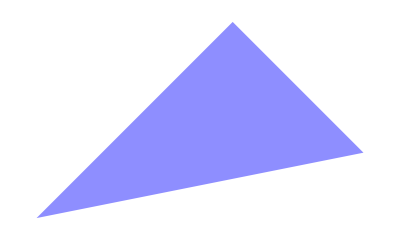

```mathematica
Graphics[{Lighter[Lighter[Blue]], Triangle[{{2,3},{-4, -3}, {6, -1}}]} ]
```

```mathematica
Rešitev : 
Trikotnik ABC je pravokoten, saj zanj velja Pitagorov izrek.
```

#### Učni list - Računanje s koreni

5. Kvadriraj.

```mathematica
Simplify[(Sqrt[5] - Sqrt[3])^2]
```

8-2 √15

```mathematica
Simplify[(2*Sqrt[3]+Sqrt[7])^2]
```

19+4 √21

```mathematica
Simplify[(Sqrt[14]+Sqrt[2])^2]
```

4 (4+√7)

```mathematica
Simplify[(Sqrt[5]-Sqrt[10])^2]
```

5 (3-2 √2)

```mathematica
Simplify[3*(Sqrt[2]+Sqrt[6])^2]
```

12 (2+√3)

```mathematica
Simplify[(Sqrt[15]-Sqrt[2])^2]
```

17-2 √30

#### Učni list - Kvadratna funkcija

5. Kolikšna je največja vrednost funkcije f(x) = -4x^2 -56x-198 in pri katerem x jo funkcija doseže?

```mathematica
f[x_] = -4x^2 - 56x - 198;
FindMaximum[f[x], {x, -100}]
```

{-2.,{x→-7.}}

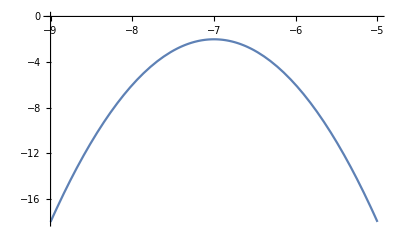

```mathematica
g = Plot[f[x], {x, -9,-5}]
```

```mathematica
Rešitev
Največja vrednost funkcije je - 2, doseže jo pri x = -7.
```

#### Učni list - Ploščine geometrijskih likov

2. Izračunaj ploščino trikotnika in zahtevani polmer, če stranice merijo:
a) a = 34 cm, b = 16 cm, c = 30 cm, R = ?
b) a = 26 cm, b = 37 cm, c  = 15 cm, r = ?
c) a = 13 cm, b = 4 cm, c = 15 cm, R = ?

```mathematica
a = 34;
b = 16;
c = 30;
s = (a+b+c)/2;
S = Sqrt[s*(s-a)*(s-b)*(s-c)];
R = (a*b*c)/(4*S);
Quantity[R, "Centimeters"]
```

17 cm

```mathematica
a = 26;
b = 37;
c = 15;
s = (a+b+c)/2;
S = Sqrt[s*(s-a)*(s-b)*(s-c)];
r = S/s;
Quantity[r, "Centimeters"]
```

4 cm

```mathematica
a = 13;
b = 4;
c = 15;
s = (a+b+c)/2;
S = Sqrt[s*(s-a)*(s-b)*(s-c)];
R = (a*b*c)/(4*S);
Quantity[R, "Centimeters"]
```

65/8 cm

#### Učni list - Polinomi 2

6. Poišči polinom tretje stopnje z vodilnim koeficientom -6 in ničlami x1 = 1, x2 = -1/2, x3 = -2.

```mathematica
a0 = -6;
a = 1;
b = -1/2;
c = -2;
p = a0*(x-a)(x-b)(x-c);
Expand[p]
```

6+9 x-9 x^2-6 x^3

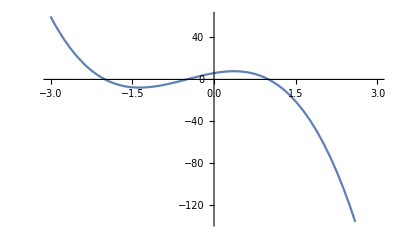

```mathematica
g = Plot[p, {x, -3, 3}]
```

#### Učni list - Statistika

10. V podjetju Alfarobot so en mesec spremljali doseganje norme pri delu. V tem času si zabeležili naslednje rezultate (v odstotkih); 90, 110, 90, 100, 110, 100, 90, 110, 120, 110, 90, 80, 90, 110, 100, 110, 100, 80, 100, 120 in 110.
a) Nariši graf doseganja norme po dnevih.
b) Izračunaj povprečno doseganje norme, določi modus ter poišči standardni odklon norme.

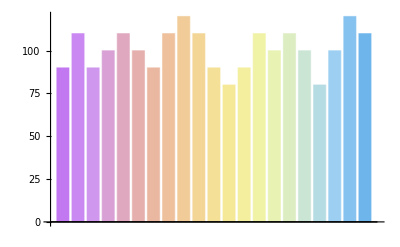

```mathematica
podatki = {90, 110, 90, 100, 110, 100, 90, 110, 120, 110, 90, 80, 90, 110, 100, 110, 100, 80, 100, 120, 110};
BarChart[podatki, ChartStyle -> "Pastel"]
```

```mathematica
N[Mean[podatki]]
StandardDeviation[podatki]
```

100.952

2 √(730/21)

#### Učni list - Odvod 2

1. Izračunaj odvod sestavljene funkcije:
a) f(x) = sin(x^3 - 5x^2 -4)
b) f(x) = ln(x^2 + 3x -7)
c) f(x) = cos lnx
d) f(x) = tan (4^x)
e) f(x) = 3^(cosx)
f) f(x) = ln cos(7x^2 + 5x -1)

```mathematica
D[Sin[x^3 - 5x^2 -4]     ,x]
D[Log[x^2 + 3x -7]       ,x]
D[Cos[Log[x]]            ,x]
D[Tan[4^x]               ,x]
D[3^(Cos[x])             ,x]
D[Log[Cos[7x^2 + 5x -1]] ,x]
```

-(10 x-3 x^2) Cos[4+5 x^2-x^3]

(3+2 x)/(-7+3 x+x^2)

-Sin[Log[x]]/x

4^x Log[4] Sec[4^x]^2

-3^Cos[x] Log[3] Sin[x]

-(-5-14 x) Tan[1-5 x-7 x^2]

#### Učni list - Aritmetična zaporedja

2. Pri danih podatkih za aritmetična zaporedja poiščite neznane količine.
a) a_n = 3n - 2                a_1 = ? a_2 = ? a_5 = ?
b ) a_1 = -7, d = 5          a_n = ? a_10 = ?

```mathematica
a1 = 3*1 -2
a2 = 3*2 -2
a5 = 3*5 -2
```

1

4

13

```mathematica
ClearAll[n]
a1 = -7;
d = 5;
a10 = a1 + 9*d
an = a1 + (n-1)*d;
Simplify[an]
```

38

-12+5 n

#### Učni list - Geometrijska zaporedja

9. V geometrijskem zaporedju s kvocientom 3 je četrti člen 54. Koliko členov moramo sešteti, da 
dobimo vsoto 242?

```mathematica
q = 3;
a4 = 54;
sn = 242;
a1 = a4/q^3;
n = Log[q, sn*(q-1)/a1 +1]
```

5

```mathematica
Rešitev:
Da dobimo vsoto 242, moramo sešteti moramo 5 členov.
```

```mathematica
SetOptions[EvaluationNotebook[],Background-> Lighter[Lighter[Lighter[Magenta]]] ]
```